```mathematica
lagrange[f_,a_,b_,n_]:=Module[{p=Abs[b-a]/(n-1),xw=Table[0,n],yw=Table[0,n],w=0,φ,w1,w2,l,m,s},
Do[ xw⟦i⟧=a+(i-1)p; yw⟦i⟧=N[f[xw⟦i⟧]],{i,n}];
Do[φ=1;
Do[φ*= (x-xw⟦k⟧)/(xw⟦i⟧-xw⟦k⟧),{k,i-1}];
Do[φ*=(x-xw⟦k⟧)/(xw⟦i⟧-xw⟦k⟧),{k,i+1,n}];
w=w+yw⟦i⟧φ, {i,n}];
w=Simplify[w];
w1=Plot[f[x],{x,a,b},PlotStyle->{Blue}];
w2=Plot[w,{x,a,b},PlotStyle->{Red,Dashed}];
l= ListPlot[Table[{xw⟦i⟧,yw⟦i⟧},{i,n}],PlotStyle->{Orange,PointSize[0.015]}];
m=Show[w1,w2,l];
s=Plot[Abs[f[x]-w],{x,a,b},PlotRange -> All];
Print[w];
Print[m];
Print[s];
Return[{m,s,w}];]
```

-1.+1.57625 x-0.493925 x^2-0.529739 x^3-0.0491561 x^4+0.0909473 x^5

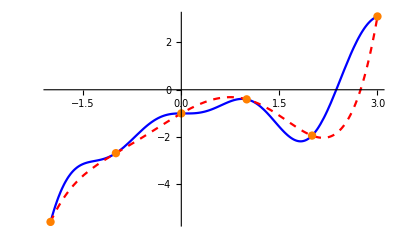

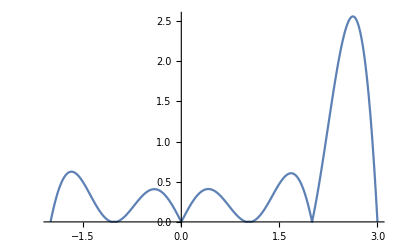

```mathematica
(*PRZYKŁAD TESTOWY*)

Clear[f];
f[x_]:=(x-Sin[2x])Cos[2x]-E^-x;
lagrange[f,-2,3,6];
```

-1.00008+0.000232051 x-0.497011 x^2+3.49696 x^3-0.0592738 x^4-3.58005 x^5+0.0364206 x^6+1.51599 x^7-0.0378458 x^8-0.334829 x^9+0.0189442 x^10+0.0415645 x^11-0.00456151 x^12-0.0023595 x^13+0.000416047 x^14

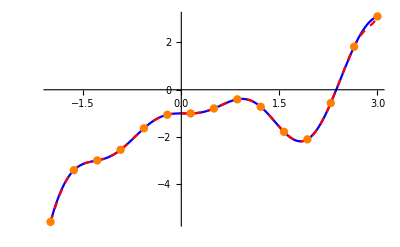

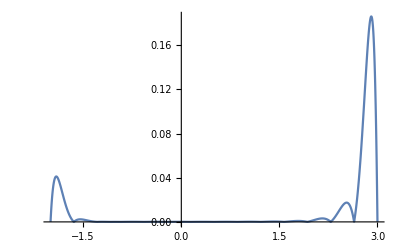

```mathematica
lagrange[f,-2,3,15];
```

-1.-7.30312×10^-7 x-0.500009 x^2+3.50003 x^3-0.041594 x^4-3.59187 x^5-0.00156523 x^6+1.53734 x^7+0.0000429804 x^8-0.35575 x^9+0.00024597 x^10+0.0528902 x^11-0.000341441 x^12-0.00558221 x^13+0.000178754 x^14+0.000422863 x^15-0.0000419712 x^16-0.0000168975 x^17+3.66629×10^-6 x^18-1.9398×10^-7 x^19

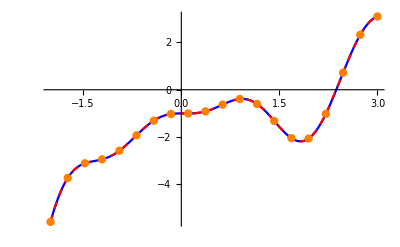

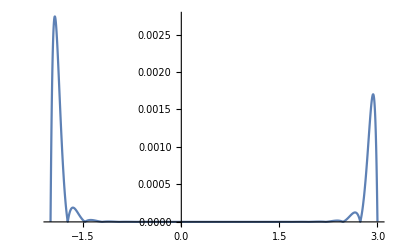

```mathematica
lagrange[f,-2,3,20];
```

Wielomian: 1/12 (132-204 x+101 x^2-18 x^3+x^4)

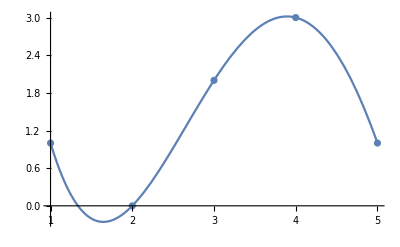

```mathematica
(*ZADANIE A*)
Clear[lagrange];
lagrange2[xa_,ya_]:=Module[{w=0,n=Length[xa]},
For[i=1,i<=n,i++,
f=1;
For[k=1,k<=i-1,k++,
f=f*(x-xa[[k]])/(xa[[i]]-xa[[k]]);
];
For[k=i+1,k<=n,k++,
f=f*(x-xa[[k]])/(xa[[i]]-xa[[k]]);
];
w=w+ya[[i]]*f;
];
wl = Simplify[w];
Print["Wielomian: ",wl];
Print[Show[Plot[wl,{x,xa[[1]],xa[[n]]}],ListPlot[Thread[{xa,ya}]]]];
Return[wl];

]

Ax1={1,2,3,4,5};
Ay1={1,0,2,3,1};
lagrange2[Ax1,Ay1];
```

```mathematica
(*ZADANIE B*)
Clear[f];
```

1.

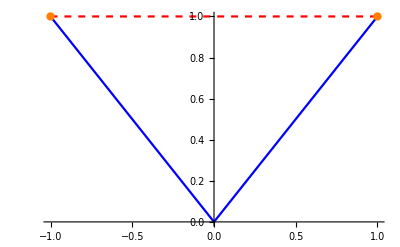

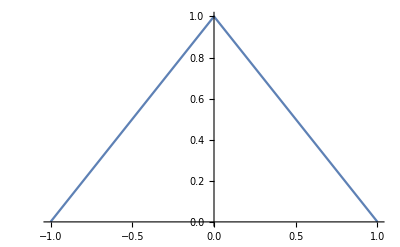

```mathematica
f[x_]:= Abs[x]
lagrange[f,-1,1,2];
```

0.+2.33333 x^2-1.33333 x^4

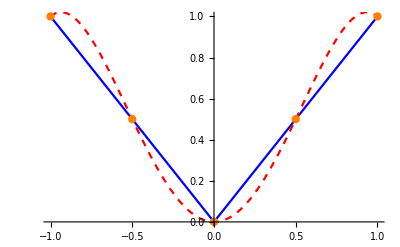

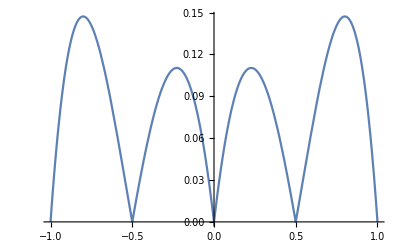

```mathematica
lagrange[f,-1,1,5];
```

0.0747681+1.66533×10^-16 x+3.03371 x^2-7.54952×10^-15 x^3-7.40588 x^4-4.52971×10^-14 x^5+9.9312 x^6-1.06581×10^-14 x^7-4.6338 x^8-1.77636×10^-15 x^9

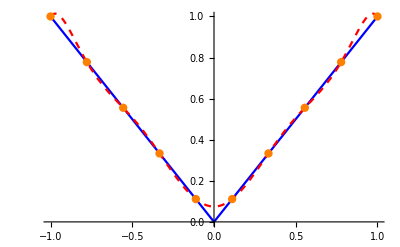

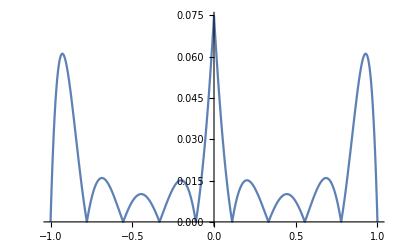

```mathematica
lagrange[f,-1,1,10];
```

0.050889+1.11022×10^-16 x+4.55729 x^2+8.32667×10^-15 x^3-27.2464 x^4-9.68114×10^-13 x^5+106.636 x^6-4.60432×10^-12 x^7-216.025 x^8+2.78533×10^-12 x^9+209.756 x^10+2.27374×10^-12 x^11-76.7289 x^12-5.68434×10^-14 x^13

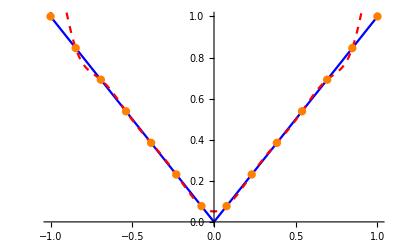

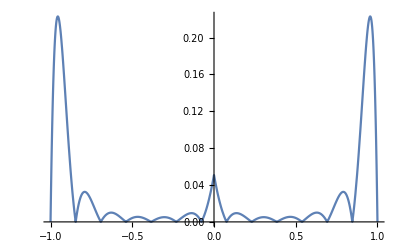

```mathematica
lagrange[f,-1,1,14];
```